```mathematica
getPropFmat[idm_]:=Module[
{Imt,Wmt},
Imt=IdentityMatrix[idm];
Wmt=1/2*(RotateLeft[Imt]+RotateRight[Imt]);
Factor[Inverse[Imt-a*Wmt]*(1-a)]
]

turnOnNums[ilt_,lng_]:=Module[
{zrs},
zrs=PadLeft[{0},lng];
zrs[[ilt]]=1;
zrs
]

turnOnSel[lng_, nsl_] :=(turnOnNums[#,lng])&/@Subsets[Range[lng],{nsl}]
allpropmat[lng_, nsl_] := Factor[getPropFmat[lng].Transpose[(turnOnNums[#,lng])&/@Subsets[Range[lng],{nsl}]]]
```

```mathematica
getPropFmat[5]
turnOnSel[5,3]
allpropmat[5,3]
```

{{(-4+2 a+a^2)/(-4-2 a+a^2),((-2+a) a)/(-4-2 a+a^2),-a^2/(-4-2 a+a^2),-a^2/(-4-2 a+a^2),((-2+a) a)/(-4-2 a+a^2)},{((-2+a) a)/(-4-2 a+a^2),(-4+2 a+a^2)/(-4-2 a+a^2),((-2+a) a)/(-4-2 a+a^2),-a^2/(-4-2 a+a^2),-a^2/(-4-2 a+a^2)},{-a^2/(-4-2 a+a^2),((-2+a) a)/(-4-2 a+a^2),(-4+2 a+a^2)/(-4-2 a+a^2),((-2+a) a)/(-4-2 a+a^2),-a^2/(-4-2 a+a^2)},{-a^2/(-4-2 a+a^2),-a^2/(-4-2 a+a^2),((-2+a) a)/(-4-2 a+a^2),(-4+2 a+a^2)/(-4-2 a+a^2),((-2+a) a)/(-4-2 a+a^2)},{((-2+a) a)/(-4-2 a+a^2),-a^2/(-4-2 a+a^2),-a^2/(-4-2 a+a^2),((-2+a) a)/(-4-2 a+a^2),(-4+2 a+a^2)/(-4-2 a+a^2)}}

{{1,1,1,0,0},{1,1,0,1,0},{1,1,0,0,1},{1,0,1,1,0},{1,0,1,0,1},{1,0,0,1,1},{0,1,1,1,0},{0,1,1,0,1},{0,1,0,1,1},{0,0,1,1,1}}

{{((-2+a) (2+a))/(-4-2 a+a^2),((-2+a) (2+a))/(-4-2 a+a^2),(-4-2 a+3 a^2)/(-4-2 a+a^2),-(4-2 a+a^2)/(-4-2 a+a^2),((-2+a) (2+a))/(-4-2 a+a^2),((-2+a) (2+a))/(-4-2 a+a^2),-(a (2+a))/(-4-2 a+a^2),((-4+a) a)/(-4-2 a+a^2),((-4+a) a)/(-4-2 a+a^2),-(a (2+a))/(-4-2 a+a^2)},{(-4-2 a+3 a^2)/(-4-2 a+a^2),((-2+a) (2+a))/(-4-2 a+a^2),((-2+a) (2+a))/(-4-2 a+a^2),((-4+a) a)/(-4-2 a+a^2),((-4+a) a)/(-4-2 a+a^2),-(a (2+a))/(-4-2 a+a^2),((-2+a) (2+a))/(-4-2 a+a^2),((-2+a) (2+a))/(-4-2 a+a^2),-(4-2 a+a^2)/(-4-2 a+a^2),-(a (2+a))/(-4-2 a+a^2)},{((-2+a) (2+a))/(-4-2 a+a^2),((-4+a) a)/(-4-2 a+a^2),-(a (2+a))/(-4-2 a+a^2),((-2+a) (2+a))/(-4-2 a+a^2),-(4-2 a+a^2)/(-4-2 a+a^2),-(a (2+a))/(-4-2 a+a^2),(-4-2 a+3 a^2)/(-4-2 a+a^2),((-2+a) (2+a))/(-4-2 a+a^2),((-4+a) a)/(-4-2 a+a^2),((-2+a) (2+a))/(-4-2 a+a^2)},{-(a (2+a))/(-4-2 a+a^2),-(4-2 a+a^2)/(-4-2 a+a^2),-(a (2+a))/(-4-2 a+a^2),((-2+a) (2+a))/(-4-2 a+a^2),((-4+a) a)/(-4-2 a+a^2),((-2+a) (2+a))/(-4-2 a+a^2),((-2+a) (2+a))/(-4-2 a+a^2),((-4+a) a)/(-4-2 a+a^2),((-2+a) (2+a))/(-4-2 a+a^2),(-4-2 a+3 a^2)/(-4-2 a+a^2)},{-(a (2+a))/(-4-2 a+a^2),((-4+a) a)/(-4-2 a+a^2),((-2+a) (2+a))/(-4-2 a+a^2),((-4+a) a)/(-4-2 a+a^2),((-2+a) (2+a))/(-4-2 a+a^2),(-4-2 a+3 a^2)/(-4-2 a+a^2),-(a (2+a))/(-4-2 a+a^2),-(4-2 a+a^2)/(-4-2 a+a^2),((-2+a) (2+a))/(-4-2 a+a^2),((-2+a) (2+a))/(-4-2 a+a^2)}}

```mathematica
firstNodePropAll5 = allpropmat[5,3][[1]]
```

{((-2+a) (2+a))/(-4-2 a+a^2),((-2+a) (2+a))/(-4-2 a+a^2),(-4-2 a+3 a^2)/(-4-2 a+a^2),-(4-2 a+a^2)/(-4-2 a+a^2),((-2+a) (2+a))/(-4-2 a+a^2),((-2+a) (2+a))/(-4-2 a+a^2),-(a (2+a))/(-4-2 a+a^2),((-4+a) a)/(-4-2 a+a^2),((-4+a) a)/(-4-2 a+a^2),-(a (2+a))/(-4-2 a+a^2)}

```mathematica
Factor[Mean[firstNodePropAll5]]
```

3/5

```mathematica
Factor[Simplify[StandardDeviation[firstNodePropAll5],a∈Reals]]
```

(2 √(2/15) √(8+4 a+3 a^2) Abs[-1+a])/Abs[-4-2 a+a^2]

```mathematica
Factor[8-12 a+3 a^2-2 a^3+3 a^4]
```

(-1+a)^2 (8+4 a+3 a^2)

```mathematica
Factor[16+16 a-4 a^2-4 a^3+a^4]
```

(-4-2 a+a^2)^2

```mathematica
a
```

```mathematica
Names["Global`*"]
```

{a,allpropmat,firstNodePropAll5,getPropFmat,idm,ilt,Imt,Imt$,lng,nsl,turnOnNums,turnOnSel,Wmt,Wmt$,zrs,zrs$}

```mathematica
clearall
```

clearall

```mathematica
Clear[a]
```

```mathematica
a = alpha + I0
```

alpha+I0

```mathematica
Clear[a]
Simplify[(-4-2 a+3 a^2)/(-4-2 a+a^2), a==1/2]
```

17/19

```mathematica
Simplify[-(4-2 a+a^2)/(-4-2 a+a^2), a==1/2]
```

13/19

```mathematica
Simplify[((-2+a) (2+a))/(-4-2 a+a^2), a==1/2]
```

15/19

```mathematica
a
```

1/2

```mathematica
Clear[a]
```

```mathematica
a
```

a

```mathematica
firstNodePropAll5 [[3]]
```

(-4-2 a+3 a^2)/(-4-2 a+a^2)

```mathematica
Factor[(firstNodePropAll5 [[3]]-Mean[firstNodePropAll5])/Simplify[StandardDeviation[firstNodePropAll5],a∈Reals]]
```

(√(6/5) (-1+a) (2+3 a) Abs[-4-2 a+a^2])/((-4-2 a+a^2) √(8+4 a+3 a^2) Abs[-1+a])

```mathematica
Factor[(firstNodePropAll5 [[3]]-Mean[firstNodePropAll5])/Simplify[StandardDeviation[firstNodePropAll5],Element[a, Reals ] && a > 0 && a < 1]]
```

(√(6/5) (2+3 a))/(√(8+4 a+3 a^2))

```mathematica
Simplify[(√(6/5) (2+3 a))/(√(8+4 a+3 a^2)), a==1]
```

√2

```mathematica
f[a_] := (√(6/5) (-1+a) (2+3 a) Abs[-4-2 a+a^2])/((-4-2 a+a^2) √(8+4 a+3 a^2) Abs[-1+a])
```

```mathematica
f[0]
```

√(3/5)

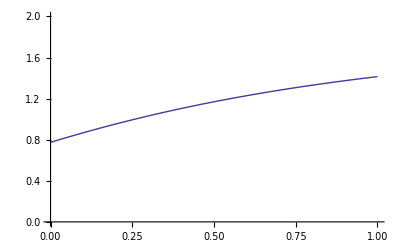

```mathematica
Plot[f[x], {x, 0, 0.99999}, PlotRange -> {0,2}]
```